Вариант 4

Задание 3

Попробуем методы Solve и NSolve

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[-5+0.7^x==Log[4-x]/Log[2],x]

NSolve[-5+0.7^x==Log[4-x]/Log[2],x]

Как видно, данные методы не работают для этого уравнения

Построим графики для нахождения корней

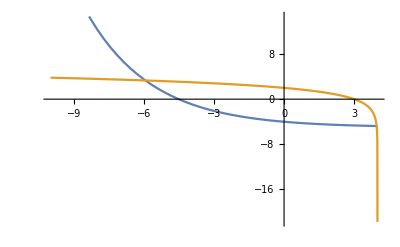

Используем метод FindRoot для нахождения корней

{x→-5.93764}

{x→3.96301}

```mathematica
"Вариант 4"

"Задание 3"

z[x_] := 0.7^x-5;
k[x_] := Log2[4-x];
"Попробуем методы Solve и NSolve"
Solve[z[x] == k[x], x]
NSolve[z[x] == k[x], x]
"Как видно, данные методы не работают для этого уравнения"
"Построим графики для нахождения корней"
Plot[{z[x], k[x]}, {x, -10, 4}]
"Используем метод FindRoot для нахождения корней"
FindRoot[z[x] == k[x], {x, -6}]
FindRoot[z[x] == k[x], {x, 3}]
```